```mathematica
outputPath=StringJoin[NotebookDirectory[],"MagnetComparison/"];
cPath=NotebookDirectory[];
dataPath=StringJoin[NotebookDirectory[],"Experimental_Data/"];

fPath=NotebookDirectory[];
μ0=4*π*10^-7;

(* Globale Anweisung zur Darstellung von Plots *)
SetOptions[{Plot,ListLinePlot,LogPlot,LogLogPlot,ListPlot,ParametricPlot,ListLogLogPlot},PlotStyle->{{Thickness[0.005],{Blue}},{Thickness[0.005],{Red}},{Thickness[0.005],{Green}},{Thickness[0.005],{Magenta}},{Thickness[0.005],{Cyan}},{Thickness[0.005],{Orange}}},BaseStyle->{FontFamily->"Times",FontSize->13,Background->None,Black},GridLines->Automatic,Frame->True,FrameStyle->Black,Background->White,ImageSize->Medium,FrameTicksStyle->Background->None,LabelStyle->Background->None];

SetOptions[{StreamDensityPlot,RegionPlot,RegionPlot3D},PlotRange->All,PlotTheme->"Classic",AspectRatio->Automatic];
```

```mathematica
(* some auxiliary symbols *)
Q[k_]:={{1,0,0},{0,1,0},{0,0,(-1)^k}}
c[k_]:=(-1)^k*h*{0,0,1}

xEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,1]])
yEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,2]])
zEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,3]])

X[k_,l_]:=xEigen[k]+(-1)^l*w
Y[k_,l_]:=yEigen[k]+(-1)^l*d
Z[k_]:=zEigen[k]

R[k_,l_,m_]:=Sqrt[X[k,l]^2+Y[k,m]^2+Z[k]^2]
```

```mathematica
(* potential *)
V=Sum[
(-1)^(k+l+m)*(
-Z[k]*ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]+X[k,l]*Log[Y[k,m]+R[k,l,m]]+Y[k,m]*Log[X[k,l]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}];
```

### x

```mathematica
DxV=Sum[
(-1)^(k+l+m)*(
-(Y[k,m]/R[k,l,m]-X[k,l]^2*Y[k,m]/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)+Log[Y[k,m]+R[k,l,m]]+X[k,l]^2/(R[k,l,m]*(Y[k,m]+R[k,l,m]))+Y[k,m]*(1+X[k,l]/R[k,l,m])/(X[k,l]+R[k,l,m])
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
D[V,x]-DxV//Simplify
```

0

Simplify expression “manually”:
Part 1:

```mathematica
Sum[
(-1)^(k+l+m)*(
-(Y[k,m]/R[k,l,m]-X[k,l]^2*Y[k,m]/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)
),
{k,1,2},{l,1,2},{m,1,2}]
```

-(((-w+x)^2 (-d+y))/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-d+y)/(√((-w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x)^2 (-d+y))/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-d+y)/(√((w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x)^2 (d+y))/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(d+y)/(√((-w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x)^2 (d+y))/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(d+y)/(√((w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x)^2 (-d+y))/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-d+y)/(√((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x)^2 (-d+y))/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-d+y)/(√((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x)^2 (d+y))/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(d+y)/(√((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x)^2 (d+y))/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(d+y)/(√((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 1.1:

```mathematica
-(((-w+x)^2 (-d+y))/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-d+y)/(√((-w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x)^2 (-d+y))/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-d+y)/(√((w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x)^2 (d+y))/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(d+y)/(√((-w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x)^2 (d+y))/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(d+y)/(√((w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))//Simplify
```

(h+z)^2 ((-d+y)/((h^2+w^2-2 w x+x^2+2 h z+z^2) √(d^2+h^2+w^2-2 w x+x^2-2 d y+y^2+2 h z+z^2))+(d-y)/((h^2+w^2+2 w x+x^2+2 h z+z^2) √((w+x)^2+(d-y)^2+(h+z)^2))-(d+y)/((h^2+w^2-2 w x+x^2+2 h z+z^2) √((w-x)^2+(d+y)^2+(h+z)^2))+(d+y)/((h^2+w^2+2 w x+x^2+2 h z+z^2) √((w+x)^2+(d+y)^2+(h+z)^2)))

Part 1.2:

```mathematica
+(((-w+x)^2 (-d+y))/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-d+y)/(√((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x)^2 (-d+y))/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-d+y)/(√((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x)^2 (d+y))/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(d+y)/(√((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x)^2 (d+y))/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(d+y)/(√((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))//Simplify
```

(h-z)^2 ((d-y)/(√((w-x)^2+(d-y)^2+(h-z)^2) (h^2+w^2-2 w x+x^2-2 h z+z^2))+(d+y)/(√((w-x)^2+(d+y)^2+(h-z)^2) (h^2+w^2-2 w x+x^2-2 h z+z^2))+(-d+y)/(√((w+x)^2+(d-y)^2+(h-z)^2) (h^2+w^2+2 w x+x^2-2 h z+z^2))-(d+y)/(√((w+x)^2+(d+y)^2+(h-z)^2) (h^2+w^2+2 w x+x^2-2 h z+z^2)))

Part 2:

```mathematica
Sum[
(-1)^(k+l+m)*(Log[Y[k,m]+R[k,l,m]]),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

Log[-d+y+√((w-x)^2+(d-y)^2+(h-z)^2)]-Log[-d+y+√((w+x)^2+(d-y)^2+(h-z)^2)]-Log[d+y+√((w-x)^2+(d+y)^2+(h-z)^2)]+Log[d+y+√((w+x)^2+(d+y)^2+(h-z)^2)]-Log[-d+y+√((w-x)^2+(d-y)^2+(h+z)^2)]+Log[-d+y+√((w+x)^2+(d-y)^2+(h+z)^2)]+Log[d+y+√((w-x)^2+(d+y)^2+(h+z)^2)]-Log[d+y+√((w+x)^2+(d+y)^2+(h+z)^2)]

Part 3 (simplification not working):

```mathematica
Sum[
(-1)^(k+l+m)*(X[k,l]^2/(R[k,l,m]*(Y[k,m]+R[k,l,m]))
),
{k,1,2},{l,1,2},{m,1,2}]
```

-(-w+x)^2/((-d+y+√((-w+x)^2+(-d+y)^2+(-h-z)^2)) √((-w+x)^2+(-d+y)^2+(-h-z)^2))+(w+x)^2/((-d+y+√((w+x)^2+(-d+y)^2+(-h-z)^2)) √((w+x)^2+(-d+y)^2+(-h-z)^2))+(-w+x)^2/((d+y+√((-w+x)^2+(d+y)^2+(-h-z)^2)) √((-w+x)^2+(d+y)^2+(-h-z)^2))-(w+x)^2/((d+y+√((w+x)^2+(d+y)^2+(-h-z)^2)) √((w+x)^2+(d+y)^2+(-h-z)^2))+(-w+x)^2/(√((-w+x)^2+(-d+y)^2+(-h+z)^2) (-d+y+√((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(w+x)^2/(√((w+x)^2+(-d+y)^2+(-h+z)^2) (-d+y+√((w+x)^2+(-d+y)^2+(-h+z)^2)))-(-w+x)^2/(√((-w+x)^2+(d+y)^2+(-h+z)^2) (d+y+√((-w+x)^2+(d+y)^2+(-h+z)^2)))+(w+x)^2/(√((w+x)^2+(d+y)^2+(-h+z)^2) (d+y+√((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 4:

```mathematica
Sum[
(-1)^(k+l+m)*(Y[k,m]*(1+X[k,l]/R[k,l,m])/(X[k,l]+R[k,l,m])
),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

(-d+y)/(√((w-x)^2+(d-y)^2+(h-z)^2))+(d-y)/(√((w+x)^2+(d-y)^2+(h-z)^2))+(-d-y)/(√((w-x)^2+(d+y)^2+(h-z)^2))+(d+y)/(√((w+x)^2+(d+y)^2+(h-z)^2))+(d-y)/(√(d^2+h^2+w^2-2 w x+x^2-2 d y+y^2+2 h z+z^2))+(-d+y)/(√((w+x)^2+(d-y)^2+(h+z)^2))+(d+y)/(√((w-x)^2+(d+y)^2+(h+z)^2))+(-d-y)/(√((w+x)^2+(d+y)^2+(h+z)^2))

### y

```mathematica
DyV=Sum[
(-1)^(k+l+m)*(
-(X[k,l]/R[k,l,m]-X[k,l]*Y[k,m]^2/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)+X[k,l]*(1+Y[k,m]/R[k,l,m])/(Y[k,m]+R[k,l,m])+Log[X[k,l]+R[k,l,m]]+Y[k,m]^2/(R[k,l,m]*(X[k,l]+R[k,l,m]))
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
D[V,y]-DyV//Simplify
```

0

Part 1:

```mathematica
Sum[
(-1)^(k+l+m)*(
-(X[k,l]/R[k,l,m]-X[k,l]*Y[k,m]^2/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)
),
{k,1,2},{l,1,2},{m,1,2}]
```

-(((-w+x) (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x) (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(w+x)/(√((w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x) (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x) (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(w+x)/(√((w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x) (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x) (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(w+x)/(√((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x) (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x) (d+y)^2)/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(w+x)/(√((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 1.1:

```mathematica
-(((-w+x) (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x) (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(w+x)/(√((w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x) (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x) (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(w+x)/(√((w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))//Simplify
```

$Aborted

Part 1.2:

```mathematica
+(((-w+x) (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x) (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(w+x)/(√((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x) (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x) (d+y)^2)/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(w+x)/(√((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))//Simplify
```

(h-z)^2 ((w-x)/(√((w-x)^2+(d-y)^2+(h-z)^2) (d^2+h^2-2 d y+y^2-2 h z+z^2))+(w+x)/(√((w+x)^2+(d-y)^2+(h-z)^2) (d^2+h^2-2 d y+y^2-2 h z+z^2))+(-w+x)/(√((w-x)^2+(d+y)^2+(h-z)^2) (d^2+h^2+2 d y+y^2-2 h z+z^2))-(w+x)/(√((w+x)^2+(d+y)^2+(h-z)^2) (d^2+h^2+2 d y+y^2-2 h z+z^2)))

Part 2:

```mathematica
Sum[
(-1)^(k+l+m)*(X[k,l]*(1+Y[k,m]/R[k,l,m])/(Y[k,m]+R[k,l,m])),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

(-w+x)/(√((w-x)^2+(d-y)^2+(h-z)^2))+(-w-x)/(√((w+x)^2+(d-y)^2+(h-z)^2))+(w-x)/(√((w-x)^2+(d+y)^2+(h-z)^2))+(w+x)/(√((w+x)^2+(d+y)^2+(h-z)^2))+(w-x)/(√(d^2+h^2+w^2-2 w x+x^2-2 d y+y^2+2 h z+z^2))+(w+x)/(√((w+x)^2+(d-y)^2+(h+z)^2))+(-w+x)/(√((w-x)^2+(d+y)^2+(h+z)^2))+(-w-x)/(√((w+x)^2+(d+y)^2+(h+z)^2))

Part 3:

```mathematica
Sum[
(-1)^(k+l+m)*(Log[X[k,l]+R[k,l,m]]),
{k,1,2},{l,1,2},{m,1,2}]
```

-Log[-w+x+√((-w+x)^2+(-d+y)^2+(-h-z)^2)]+Log[w+x+√((w+x)^2+(-d+y)^2+(-h-z)^2)]+Log[-w+x+√((-w+x)^2+(d+y)^2+(-h-z)^2)]-Log[w+x+√((w+x)^2+(d+y)^2+(-h-z)^2)]+Log[-w+x+√((-w+x)^2+(-d+y)^2+(-h+z)^2)]-Log[w+x+√((w+x)^2+(-d+y)^2+(-h+z)^2)]-Log[-w+x+√((-w+x)^2+(d+y)^2+(-h+z)^2)]+Log[w+x+√((w+x)^2+(d+y)^2+(-h+z)^2)]

Part 4:

```mathematica
Sum[
(-1)^(k+l+m)*(Y[k,m]^2/(R[k,l,m]*(X[k,l]+R[k,l,m]))),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

$Aborted

### z

```mathematica
DzV=Sum[
(-1)^(l+m)*(
-ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]+
(X[k,l]*Y[k,m]/R[k,l,m]/Z[k]+X[k,l]*Y[k,m]*Z[k]/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)
+X[k,l]*Z[k]/(R[k,l,m]*(Y[k,m]+R[k,l,m]))+Y[k,m]*Z[k]/(R[k,l,m]*(X[k,l]+R[k,l,m]))
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
D[V,z]-DzV//Simplify
```

0

Part 1:

```mathematica
Sum[
(-1)^(l+m)*(
-ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

ArcTan[((w+x) (d-y))/(√((w+x)^2+(d-y)^2+(h-z)^2) (h-z))]+ArcTan[((w-x) (d+y))/(√((w-x)^2+(d+y)^2+(h-z)^2) (h-z))]-ArcTan[((-w+x) (-d+y))/(√((w-x)^2+(d-y)^2+(h-z)^2) (-h+z))]-ArcTan[((w+x) (d+y))/(√((w+x)^2+(d+y)^2+(h-z)^2) (-h+z))]+ArcTan[((w-x) (d-y))/((h+z) √((w-x)^2+(d-y)^2+(h+z)^2))]+ArcTan[((w+x) (d-y))/((h+z) √((w+x)^2+(d-y)^2+(h+z)^2))]+ArcTan[((w-x) (d+y))/((h+z) √((w-x)^2+(d+y)^2+(h+z)^2))]+ArcTan[((w+x) (d+y))/((h+z) √((w+x)^2+(d+y)^2+(h+z)^2))]

Part 2:

```mathematica
Sum[
(-1)^(l+m)*((X[k,l]*Y[k,m]/R[k,l,m]/Z[k]+X[k,l]*Y[k,m]*Z[k]/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)),
{k,1,2},{l,1,2},{m,1,2}]
```

(((-w+x) (-d+y))/(√((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z))+((-w+x) (-d+y) (-h-z))/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x) (-d+y))/(√((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z))+((w+x) (-d+y) (-h-z))/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))-(((-w+x) (d+y))/(√((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z))+((-w+x) (d+y) (-h-z))/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x) (d+y))/(√((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z))+((w+x) (d+y) (-h-z))/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x) (-d+y) (-h+z))/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))+((-w+x) (-d+y))/((-h+z) √((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x) (-d+y) (-h+z))/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))+((w+x) (-d+y))/((-h+z) √((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x) (d+y) (-h+z))/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))+((-w+x) (d+y))/((-h+z) √((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x) (d+y) (-h+z))/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))+((w+x) (d+y))/((-h+z) √((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 2.1:

```mathematica
(((-w+x) (-d+y))/(√((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z))+((-w+x) (-d+y) (-h-z))/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x) (-d+y))/(√((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z))+((w+x) (-d+y) (-h-z))/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))-(((-w+x) (d+y))/(√((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z))+((-w+x) (d+y) (-h-z))/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x) (d+y))/(√((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z))+((w+x) (d+y) (-h-z))/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))//Simplify
```

(h+z) (-((w-x) (d-y) (d^2+2 h^2+w^2-2 w x+x^2-2 d y+y^2+4 h z+2 z^2))/((h^2+w^2-2 w x+x^2+2 h z+z^2) (d^2+h^2-2 d y+y^2+2 h z+z^2) √(d^2+h^2+w^2-2 w x+x^2-2 d y+y^2+2 h z+z^2))-((w+x) (d-y) (d^2+2 h^2+w^2+2 w x+x^2-2 d y+y^2+4 h z+2 z^2))/((h^2+w^2+2 w x+x^2+2 h z+z^2) (d^2+h^2-2 d y+y^2+2 h z+z^2) √((w+x)^2+(d-y)^2+(h+z)^2))-((w-x) (d+y) (d^2+2 h^2+w^2-2 w x+x^2+2 d y+y^2+4 h z+2 z^2))/((h^2+w^2-2 w x+x^2+2 h z+z^2) (d^2+h^2+2 d y+y^2+2 h z+z^2) √((w-x)^2+(d+y)^2+(h+z)^2))-((w+x) (d+y) (d^2+2 h^2+w^2+2 w x+x^2+2 d y+y^2+4 h z+2 z^2))/((h^2+w^2+2 w x+x^2+2 h z+z^2) (d^2+h^2+2 d y+y^2+2 h z+z^2) √((w+x)^2+(d+y)^2+(h+z)^2)))

Part 2.2:

```mathematica
+(((-w+x) (-d+y) (-h+z))/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))+((-w+x) (-d+y))/((-h+z) √((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x) (-d+y) (-h+z))/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))+((w+x) (-d+y))/((-h+z) √((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x) (d+y) (-h+z))/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))+((-w+x) (d+y))/((-h+z) √((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x) (d+y) (-h+z))/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))+((w+x) (d+y))/((-h+z) √((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))//Simplify
```

(h-z) (-((w-x) (d-y) (d^2+2 h^2+w^2-2 w x+x^2-2 d y+y^2-4 h z+2 z^2))/(√((w-x)^2+(d-y)^2+(h-z)^2) (h^2+w^2-2 w x+x^2-2 h z+z^2) (d^2+h^2-2 d y+y^2-2 h z+z^2))-((w+x) (d-y) (d^2+2 h^2+w^2+2 w x+x^2-2 d y+y^2-4 h z+2 z^2))/(√((w+x)^2+(d-y)^2+(h-z)^2) (h^2+w^2+2 w x+x^2-2 h z+z^2) (d^2+h^2-2 d y+y^2-2 h z+z^2))-((w-x) (d+y) (d^2+2 h^2+w^2-2 w x+x^2+2 d y+y^2-4 h z+2 z^2))/(√((w-x)^2+(d+y)^2+(h-z)^2) (h^2+w^2-2 w x+x^2-2 h z+z^2) (d^2+h^2+2 d y+y^2-2 h z+z^2))-((w+x) (d+y) (d^2+2 h^2+w^2+2 w x+x^2+2 d y+y^2-4 h z+2 z^2))/(√((w+x)^2+(d+y)^2+(h-z)^2) (h^2+w^2+2 w x+x^2-2 h z+z^2) (d^2+h^2+2 d y+y^2-2 h z+z^2)))

Part 3 (simplification not possible):

```mathematica
Sum[
(-1)^(l+m)*(X[k,l]*Z[k]/(R[k,l,m]*(Y[k,m]+R[k,l,m]))),
{k,1,2},{l,1,2},{m,1,2}]
```

((-w+x) (-h-z))/((-d+y+√((-w+x)^2+(-d+y)^2+(-h-z)^2)) √((-w+x)^2+(-d+y)^2+(-h-z)^2))-((w+x) (-h-z))/((-d+y+√((w+x)^2+(-d+y)^2+(-h-z)^2)) √((w+x)^2+(-d+y)^2+(-h-z)^2))-((-w+x) (-h-z))/((d+y+√((-w+x)^2+(d+y)^2+(-h-z)^2)) √((-w+x)^2+(d+y)^2+(-h-z)^2))+((w+x) (-h-z))/((d+y+√((w+x)^2+(d+y)^2+(-h-z)^2)) √((w+x)^2+(d+y)^2+(-h-z)^2))+((-w+x) (-h+z))/(√((-w+x)^2+(-d+y)^2+(-h+z)^2) (-d+y+√((-w+x)^2+(-d+y)^2+(-h+z)^2)))-((w+x) (-h+z))/(√((w+x)^2+(-d+y)^2+(-h+z)^2) (-d+y+√((w+x)^2+(-d+y)^2+(-h+z)^2)))-((-w+x) (-h+z))/(√((-w+x)^2+(d+y)^2+(-h+z)^2) (d+y+√((-w+x)^2+(d+y)^2+(-h+z)^2)))+((w+x) (-h+z))/(√((w+x)^2+(d+y)^2+(-h+z)^2) (d+y+√((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 4:

```mathematica
Sum[
(-1)^(l+m)*(Y[k,m]*Z[k]/(R[k,l,m]*(X[k,l]+R[k,l,m]))),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

$Aborted

### plot

```mathematica
H=-Grad[V,{x,y,z}];
```

```mathematica
pady=2;
padz=2;

wVal=1/2;
dVal=1/2;
hVal=3;
pars={M0->1,w->wVal,d->dVal,h->hVal,x->0};
Hplot[x_,z_]=H/.pars;
bar=Rectangle[{-dVal-pady,-hVal-padz},{dVal+pady,hVal+padz}];

barMagnetBoundary=Line[{{-dVal,-hVal},{-dVal,hVal},{dVal,hVal},{dVal,-hVal},{-dVal,-hVal}}];
```

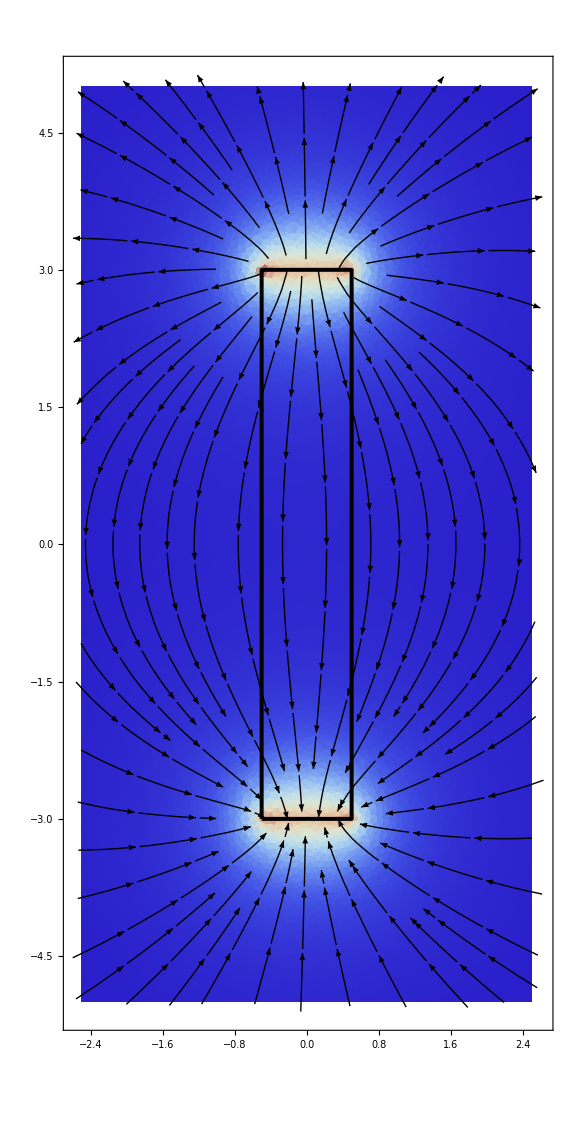

```mathematica
Show[
StreamDensityPlot[Evaluate@Hplot[y,z][[{2,3}]],{y,z}∈bar,StreamStyle->Black,StreamColorFunction->None,ColorFunction->ColorData["ThermometerColors"],AspectRatio->Automatic,StreamScale->0.12],
RegionPlot[barMagnetBoundary,BoundaryStyle->{Thickness[0.005]}],
ImageSize->Large
]
```